NALOGA 1:

```mathematica
v0 = {10, 3}
GG= 9.81
H = 10
a = {0, -GG}
x0 = {0, H}
```

{10,3}

9.81

10

{0,-9.81}

{0,10}

```mathematica
v[t_]:=v0+a *t 
(*v[t_]:={v0[[1]],v0[[2]]-GG*t*)
X[t_] :=x0 + v0 * t +(a*t^2)/2
```

```mathematica
v[1]
```

{10,-6.81}

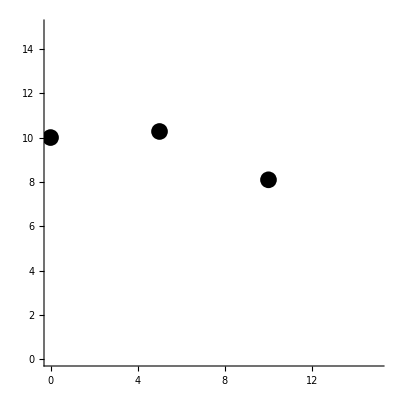

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]}
Graphics[{SlikaTocke[0],SlikaTocke[0.5],SlikaTocke[1]}, Axes->True, PlotRange->{{0,15},{0,15}}, AspectRatio->Automatic]
```

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,3}]
```

```mathematica
SlikaVektorja[t_] := Arrow[{X[t],X[t], v[t]}]
```

```mathematica
Manipulate[Graphics[{SlikaTocke[t],Arrow[{X[t], X[t]+v[t]}]}, Axes->True, PlotRange->{ {-1, domet +3},{-1, NajvišjeTočka + 3}}, AspectRatio-> Automatic],{t, 0, časLeta}
]
```

Izračunamo čas, ko žogica doseže najvišjo točko, ter njeno višino.

```mathematica
Cas=Solve[v[t][[2]]==0,t]
```

{{t→0.30581}}

```mathematica
t/.Cas
```

```mathematica
TCas=0.3058103975535168;
X[TCas];
```

```mathematica
NajvišjeTočka=X[TCas][[2]]
```

10.4587

Izračunamo čas padca žoge in točko kjer pade.

```mathematica
CasPadca=Solve[Last[X[t]] == 0 && t>0, t]
```

{{t→1.76604}}

```mathematica
CasLeta=1.7660350319649323;
```

```mathematica
X[CasLeta];
```

```mathematica
TočkaPadca=X[CasLeta][[1]]
```

17.6604

NALOGA 2:

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}];
Slika[Ravnina[n_, v_]] :=Hyperplane[n, v]
Format[r_Ravnina] := Graphics3D[Slika[r]]
```

```mathematica
r111
```

-Graphics3D-

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Ustvarimo ravnine, ki gredo skozi točko 0.

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}];
ry=Ravnina[{0, 1, 0}, {0, 0, 0}];
rz=Ravnina[{0, 0, 1}, {0, 0, 0}];
```

```mathematica
ravnine={r111,rx,ry,rz};
```

```mathematica
Graphics3D[Map[{Slika[#],SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

NALOGA 3:

```mathematica
ClearAll[AA, BB, CC, DD, n, v,Ravnina, SlikaNormale]
```

```mathematica
AA = {3,0,0}
BB = {0,6,0}
CC = {0,0,2}
DD = {4,5,1}
```

{2,0,0}

{0,3,0}

{0,0,6}

{2,3,8}

```mathematica
Piramida = {AA,BB,CC,DD}
```

{{2,0,0},{0,3,0},{0,0,6},{2,3,8}}

```mathematica
n = BB-AA
v = CC-AA
```

{-2,3,0}

{-2,0,6}

```mathematica
Ravnina=[n_,v_]
```

```mathematica
SlikaNormale[Ravnina[n_,v_]]:=Arrow[{v,v+n}]
Graphics3D[SlikaNormale[Ravnina]]
```

```mathematica
Graphics3D[Tetrahedron[Piramida]]
```

-Graphics3D-